Estudo de ϕ:

```mathematica
Solve[1+4u^2/o^4+8r/o^2-4u/o^2==0,u]
```

{{u→1/2 o (o-2 ⅈ √2 √r)},{u→1/2 o (o+2 ⅈ √2 √r)}}

0.03

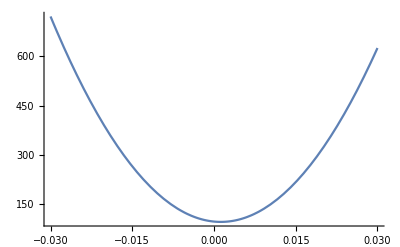

```mathematica
o=0.05;
r=0.03
Plot[1+4u^2/o^4+8r/o^2-4u/o^2,{u,-r,r}]
```

```mathematica
ϕ[u_,o_,r_]:=Sqrt[1+4u^2/o^4+8r/o^2-4u/o^2];
d1[μ_,σ_,r_]:=1/2-μ/σ^2+Sqrt[(1/2-μ/σ^2)^2+2r/σ^2];
```

```mathematica
Solve[(d1[μ,σ,r]-1)d1[μ,σ,r]ϕ[μ,σ,r]σ^2-2(r-μ)==0,r]
```

{{r→μ}}